```mathematica
(* 
implements naive Gauss--Legendre quadrature based on https://mathworld.wolfram.com/Legendre-GaussQuadrature.html 

the abscissas are the zeroes of the n-th Legendre poly

NOTE: take n ≤ 45 to avoid numerical errors

the weights are computed according to eq. (13) here: https://mathworld.wolfram.com/Legendre-GaussQuadrature.html

the quadrature function returns tuple {x,w} = {abscissas, weights} *)
GaussLegendreQuadratureWeightsNaive[a_,b_,m_]:=Module[{x,w},
x=Table[NSolve[LegendreP[m,z]==0,z][[i]][[1]][[2]],{i,1,m}];
w=Table[2 (1-x[[i]]^2)/((m+1)^2 LegendreP[m+1,x[[i]]]^2),{i,1,m}];
(* above are x's, w's for interval [-1, 1]; now I shift *)
x=(b-a)*x/2+(a+b)/2;
w=(b-a)*w/2;
Return[{x,w}]
];
```

```mathematica
(* implements Gauss--Legendre weights according to the Bornemann paper Appendix A.1 

NOTE: I am using this below for computing Fredholm dets *)
GaussLegendreQuadratureWeights[a_,b_,m_]:=Module[{k,beta,T,w,x,evals,evecs},
k=Table[i,{i,1,m-1}];
beta=k/Sqrt[(2*k-1) (2*k+1)]//N;
T=DiagonalMatrix[beta,-1]+DiagonalMatrix[beta,1];
{evals,evecs}=Eigensystem[T];
x=(evals+1)/2;
x=(1-x)*a+x*b;
w=(b-a)*Transpose[evecs][[1]]^2;
Return[{x,w}]
];
```

```mathematica
(* Test the two methods give similar results by computing the L^2 norms of xn-xb and wn-wb *)
{xn,wn}=GaussLegendreQuadratureWeightsNaive[0,1,7];
{xb,wb}=GaussLegendreQuadratureWeights[0,1,7];
(Sort[xn]-Sort[xb]).(Sort[xn]-Sort[xb])
(Sort[wn]-Sort[wb]).(Sort[wn]-Sort[wb])
```

3.86419×10^-30

4.45525×10^-30

```mathematica
(* defines the Airy kernel and additional functions to change interval to [0, 1] *)
(* Airy 2 Kernel defined on (s, ∞) *)
Airy2Kernel[x_,y_]:=If[x≠y,(AiryAi[x] AiryAiPrime[y]-AiryAiPrime[x] AiryAi[y])/(x-y),AiryAiPrime[x]^2-x AiryAi[x]^2];
Airy2KernelInt[x_,y_]:=NIntegrate[AiryAi[x+t] AiryAi[y+t],{t,0,∞}];

(* Airy 2 Kernel defined on (s, ∞) *)
Airy1Kernel[x_,y_]:=AiryAi[x+y];

(* function to map (s, ∞)->(0, 1), as Bornemann suggests *)
ϕ[s_,ξ_]:=s+10 Tan[Pi ξ/2];
(* dϕ/dξ, which for some reason has to be put by hand *)
dϕ[s_,ξ_]:= 5 Pi Sec[Pi ξ/2]^2; 

(* Airy kernels modified, based on Bornemann's idea of taking
(s, ∞) to (0, 1) *)
KernelMod[K_,s_,ξ_,η_]:=Sqrt[dϕ[s,ξ]*dϕ[s,η]]*K[ϕ[s,ξ],ϕ[s,η]];
```

```mathematica
(* precompute quadrature rules here *)
QuadratureRule:=GaussLegendreQuadratureWeights;
Clear[a,b,m];
a=0;b=1;m=15;
QuadratureRule[a,b,m];
```

```mathematica
(* computes the actual Fredholm determinant *)

(* original definition of Bornemann, no s dependence here *)
FredholmDet[K_,z_,a_,b_,
,m_]:=Module[{x,w},{x,w}=QuadratureRule[a,b,m];w=Sqrt[w];Det[IdentityMatrix[m]+z (Transpose[{w}].{w}) Outer[K,x,x]]];

(* computes Fredholm det on infinite (s, ∞) by mapping it into finite interval [a,b] which is often [0,1] in practice

NOTE: assumes K depends on s 
*)
FredholmDetInf[K_,z_,a_,b_,s_
,m_]:=Module[{x,w},{x,w}=QuadratureRule[a,b,m];w=Sqrt[w];Det[IdentityMatrix[m]+z (Transpose[{w}].{w}) Outer[KernelMod[K,s,#1,#2]&,x,x]]];
```

```mathematica
(* definining my own GOE, GUE with values a=0, b=1, m=15 as above *)

(* GUE first, three versions based on three different versions of writing the Airy 2 kernel *)
(* based on the Christoffel--Darboux-like kernel *)
FGUEa[s_]:=FredholmDetInf[Airy2Kernel,-1.0,a,b,s,m];
(* based on the integral kernel*)
FGUEb[s_]:=FredholmDetInf[Airy2KernelInt,-1.0,a,b,s,m];

(* the case of GOE, Sasamoto formula 
NOTE: s is divided by 2 *)
FGOE[s_]:=FredholmDetInf[Airy1Kernel,-1.0,a,b,s/2,m];

(* try some basic examples *)
{FGUEa[-3.]//Quiet,FGUEa[-1.77]//Quiet,FGUEa[3.]//Quiet}
{FGUEb[-3.]//Quiet,FGUEb[-1.77]//Quiet,FGUEb[3.]//Quiet}
{FGOE[-3.]//Quiet,FGOE[-1.2]//Quiet,FGOE[3.]//Quiet}
```

{0.0803205,0.515497,0.999997}

{0.0803205,0.515497,0.999997}

{0.0695915,0.52172,0.998293}

```mathematica
(* Testing the difference between our implementation and Mathematica's built-in 

in L^∞ norm for a change *)

ss=Table[i,{i,-3.,3.-1/16.,1/16.}]; (* eval at these pts *)

Print["FGUE max diff"]
myvalsGUE=Table[FGUEb[s]//Quiet,{s,ss}];
mathvalsGUE=Table[CDF[TracyWidomDistribution[2],s],{s,ss}];
Max[Abs[(myvalsGUE-mathvalsGUE)]]
(*Print["FGOE max diff"] 
myvalsGOE=Table[FGOE[s]//Quiet,{s,ss}];
mathvalsGOE=Table[CDF[TracyWidomDistribution[1],s],{s,ss}];
Max[Abs[(myvalsGOE-mathvalsGOE)]]*)
```

FGUE max diff

2.44542×10^-6

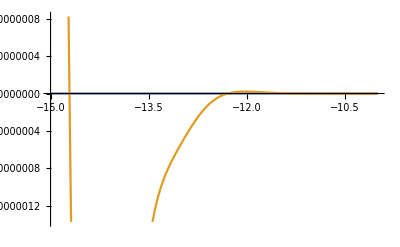

```mathematica
Plot[{CDF[TracyWidomDistribution[2],s],FGUEa[s]//Quiet},{s,-15,-10},Axes->{False,True}]
```

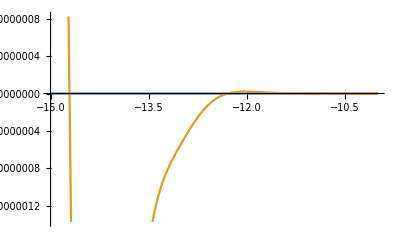

```mathematica
Plot[{CDF[TracyWidomDistribution[2],s],FGUEb[s]//Quiet},{s,-15,-10},Axes->{False,True}]
```

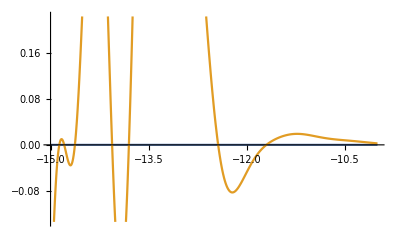

```mathematica
Plot[{CDF[TracyWidomDistribution[1],s],FGOE[s]//Quiet},{s,-15,-10},Axes->{False,True}]
```